# Bs -> mumu

```mathematica
Clear[K]
```

```mathematica
(*constants - an f at the end signifies a fixed value*)
aq2f = .04;
aq3f = 1;
al2f = 2.;
mqdiff = 700;
mldiff = 200;
GF = 1.16*^-5;
aEM = 1/137;
lambda = 0.22;
C9low1f = -0.71;
C9high1f = -0.35;
C9low2f = -0.91;
C9high2f = -0.18;
bsMixf = 2.5*^-11;
```

```mathematica
(*loop functions*)
xfunc[M_,m_]:=M^2/m^2;
Kshort[m_,c_]:= (1-xfunc[m+c,m]+xfunc[m+c,m]^2Log[xfunc[m+c,m]])/(xfunc[m+c,m]-1)^2;
Kder[m_,c_]:=(-1+xfunc[m+c,m]^2-2*xfunc[m+c,m]*Log[xfunc[m+c,m]])/(xfunc[m+c,m]-1)^3
Klong[m_,cq_,cl_]:= (Kshort[m,cq]-Kshort[m,cl])/(xfunc[m+cq,m]-xfunc[m+cl,m])
```

```mathematica
preA=1/(128Pi^ 2);
preB=5/(384Pi^ 2);
weak=4*GF/Sqrt[2]*(-1)*lambda^2*aEM/(4Pi);
```

```mathematica
(*a23(m,Mq,Ml)*)
fa23[pre_,C_,m_,cq_,cl_]:=C*weak/pre * m^2 /al2f^2 * 1/Klong[m,cq,cl];
```

```mathematica
fa23BsMix[pre_,m_,cq_]:=bsMixf*m^2/(pre *Kder[m,cq])
```

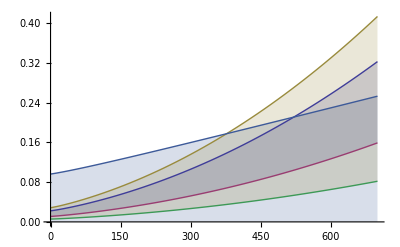

```mathematica
Plot[{fa23[preB,C9low1f,m,mqdiff,mldiff],fa23[preB,C9high1f,m,mqdiff,mldiff],fa23[preB,C9low2f,m,mqdiff,mldiff],fa23[preB,C9high2f,m,mqdiff,mldiff],Sqrt[fa23BsMix[preB,m,mqdiff]]},{m,0,700},Filling-> {1->{2},3->{4},5->Bottom}]
```

```mathematica
Plot[Sqrt[fa23BsMix[m,mqdiff]],{m,0,1000}];
```